```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY196/sec_int_data/675nm.dat"]
```

{{1.64105,0.181571},{1.57964,0.183571},{1.51907,0.201634},{1.47433,0.201961},{1.70936,0.189049},{1.78557,0.187309}}

0.26971-0.0487348 x

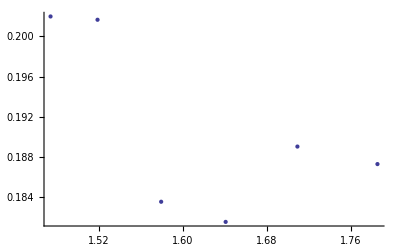

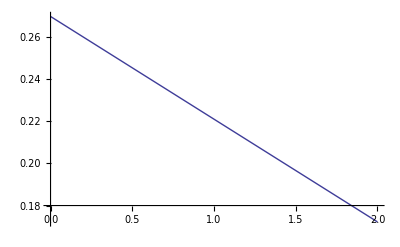

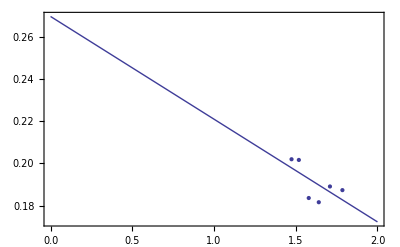

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```